## The classical ground state of zigzag phase for alpha-RuCl3

```mathematica
pKxy=-5.5;
pKz=−5.5;
pΓxy=7.6;
pΓz=7.6;
pθ=ArcTan[-2Sqrt[2] pΓxy/(pKxy+pKz-pΓz)]/2+Pi/2;
pϕ=Pi/4;
pJ=2.17;
```

```mathematica
H0[θ_,ϕ_]:=pKxy Sin[θ]^2-pKz Cos[θ]^2+pΓxy Sin[2 θ](Sin[ϕ]+Cos[ϕ])-pΓz Sin[2 ϕ] Sin[θ]^2
```

```mathematica
θ1=ArcTan[-2Sqrt[2] pΓxy/(pKxy+pKz-pΓz)]/2;
θ2=ArcTan[-2Sqrt[2] pΓxy/(pKxy+pKz-pΓz)]/2+Pi/2;
```

```mathematica
plot=Plot3D[H0[x,y],{x,0,Pi},{y,0,2Pi}];
p1=Graphics3D[{Red,PointSize[0.05],Point[{θ1,Pi/4,H0[θ1,Pi/4]}]}];
p2=Graphics3D[{Blue,PointSize[0.05],Point[{θ2,Pi/4,H0[θ2,Pi/4]}]}];
Show[plot,p1,p2]
```

-Graphics3D-

## The Spin Wave Function

#### Local coordinate for spins in ground state

```mathematica
Z[1]={Sin[θ1]Cos[ϕ1],Sin[θ1]Sin[ϕ1],Cos[θ1]};
Z[2]={Sin[θ2]Cos[ϕ2],Sin[θ2]Sin[ϕ2],Cos[θ2]};
Z[3]=-{Sin[θ3]Cos[ϕ3],Sin[θ3]Sin[ϕ3],Cos[θ3]};
Z[4]=-{Sin[θ4]Cos[ϕ4],Sin[θ4]Sin[ϕ4],Cos[θ4]};
```

```mathematica
For[i=1,i≤4,i++,S[i]=Z[i]/2]
```

```mathematica
MatrixForm[IdentityMatrix[3]]
```

```mathematica
BJ=J({{1, 0, 0}, {0, 1, 0}, {0, 0, 1}});
```

```mathematica
BX=({{Kxy, 0, 0}, {0, 0, Γxy}, {0, Γxy, 0}})+BJ;
BY=({{0, 0, Γxy}, {0, Kxy, 0}, {Γxy, 0, 0}})+BJ;
BZ=({{0, Γz, 0}, {Γz, 0, 0}, {0, 0, Kz}})+BJ;
H=h{1,1,0};
ZM=Sum[H.S[i],{i,1,4}];
```

```mathematica
hamiltonian=Simplify[S[1].BY.S[2]+Exp[-I qb]S[1].BX.S[2]+Exp[-I qa-I qb]S[1].BZ.S[4]+S[2].BZ.S[3]+S[3].BY.S[4]+Exp[-I qb]S[3].BX.S[4]+ZM];
```

```mathematica
FullSimplify[hamiltonian]
```

```mathematica
HH[Kxy_,Kz_,Γxy_,Γz_,J_,h_,qa_,qb_,θ1_,θ2_,θ3_,θ4_,ϕ1_,ϕ2_,ϕ3_,ϕ4_]:=1/4 (-(J+Kz) Cos[θ2] Cos[θ3]+2 h Cos[ϕ1] Sin[θ1]+Cos[θ2] (J Cos[θ1]+Γxy Cos[ϕ1] Sin[θ1])+2 h Cos[ϕ2] Sin[θ2]+Cos[ϕ2] (Γxy Cos[θ1]+J Cos[ϕ1] Sin[θ1]) Sin[θ2]-2 h Cos[ϕ3] Sin[θ3]+Cos[θ4] (J Cos[θ3]+Γxy Cos[ϕ3] Sin[θ3])-2 h Cos[ϕ4] Sin[θ4]+Cos[ϕ4] (Γxy Cos[θ3]+J Cos[ϕ3] Sin[θ3]) Sin[θ4]+2 h Sin[θ1] Sin[ϕ1]+2 h Sin[θ2] Sin[ϕ2]+(J+Kxy) Sin[θ1] Sin[θ2] Sin[ϕ1] Sin[ϕ2]-Cos[ϕ3] Sin[θ2] Sin[θ3] (J Cos[ϕ2]+Γz Sin[ϕ2])+ⅇ^(-ⅈ qb) (Cos[θ1] (J Cos[θ2]+Γxy Sin[θ2] Sin[ϕ2])+Sin[θ1] ((J+Kxy) Cos[ϕ1] Cos[ϕ2] Sin[θ2]+Sin[ϕ1] (Γxy Cos[θ2]+J Sin[θ2] Sin[ϕ2])))-2 h Sin[θ3] Sin[ϕ3]-Sin[θ2] Sin[θ3] (Γz Cos[ϕ2]+J Sin[ϕ2]) Sin[ϕ3]-2 h Sin[θ4] Sin[ϕ4]+(J+Kxy) Sin[θ3] Sin[θ4] Sin[ϕ3] Sin[ϕ4]+ⅇ^(-ⅈ qb) (Cos[θ3] (J Cos[θ4]+Γxy Sin[θ4] Sin[ϕ4])+Sin[θ3] ((J+Kxy) Cos[ϕ3] Cos[ϕ4] Sin[θ4]+Sin[ϕ3] (Γxy Cos[θ4]+J Sin[θ4] Sin[ϕ4])))+ⅇ^(-ⅈ (qa+qb)) (-(J+Kz) Cos[θ1] Cos[θ4]-Sin[θ1] Sin[θ4] (J Cos[ϕ1-ϕ4]+Γz Sin[ϕ1+ϕ4])))
```

```mathematica
pKxy=-5.5;
pKz=−5.5;
pΓxy=7.6;
pΓz=7.6;
pJ=-0.5;
ph=0.63;
phx=0.63;
phy=0.63;
phz=0.0;
pθ=ArcTan[-2Sqrt[2] pΓxy/(pKxy+pKz-pΓz)]/2+Pi/2;
pϕ=Pi/4;
```

```mathematica
ff[θ1_,θ2_,θ3_,θ4_,ϕ1_,ϕ2_,ϕ3_,ϕ4_]:=HH[pKxy,pKz,pΓxy,pΓz,pJ,ph,0,0,θ1,θ2,θ3,θ4,ϕ1,ϕ2,ϕ3,ϕ4]
```

```mathematica
FindMinimum[{ff[θ1,θ2,θ3,θ4,ϕ1,ϕ2,ϕ3,ϕ4],0<θ1<Pi&&0<θ2<Pi&&0<θ3<Pi&&0<θ4<Pi&&0<ϕ1<2Pi&&0<ϕ2<2Pi&&0<ϕ3<2Pi&&0<ϕ4<2Pi},{{θ1,pθ+0.8},{θ2,pθ-0.8},{θ3,pθ+0.5},{θ4,pθ-0.5},{ϕ1,pϕ+0.5},{ϕ2,pϕ-0.5},{ϕ3,pϕ+0.8},{ϕ4,pϕ-0.8}}]
```

```mathematica
{-9.269641483297866,{2.03656029925716,2.0365603432473707,1.965700084320978,1.9657000907751268,0.7853986629711207,0.785398603735745,0.7853980422865247,0.7853980310948881}}
```

```mathematica
{-9.019042675954008,{2.034892635748297,2.0348926292834877,1.9672612729295227,1.9672612545940649,0.7853990028285721,0.7853990154801782,0.7853977410603447,0.7853977585041778}}
```

```mathematica
{pθ1,pθ2,pθ3,pθ4,pϕ1,pϕ2,pϕ3,pϕ4}=SetPrecision[{2.03656029925716,2.0365603432473707,1.965700084320978,1.9657000907751268,0.7853986629711207,0.785398603735745,0.7853980422865247,0.7853980310948881},53]
```

{2.03656029925716008932568001910112798213958740234375,2.03656034324737067464639039826579391956329345703125,1.9657000843209779805675907482509501278400421142578125,1.9657000907751267515521931272814981639385223388671875,0.7853986629711207090309699196950532495975494384765625,0.7853986037357449934148689862922765314579010009765625,0.78539804228652465578619512598379515111446380615234375,0.78539803109488814936156586554716341197490692138671875}

```mathematica
pθ1
```

1.97777

```mathematica
Clear[Z,X,Y,S,hamiltonian,S0,SX,SY,BJ,BX,BY,BZ,H,ZM]
```

```mathematica
Z[1]={Sin[θ1]Cos[ϕ1],Sin[θ1]Sin[ϕ1],Cos[θ1]};
Z[2]={Sin[θ2]Cos[ϕ2],Sin[θ2]Sin[ϕ2],Cos[θ2]};
Z[3]=-{Sin[θ3]Cos[ϕ3],Sin[θ3]Sin[ϕ3],Cos[θ3]};
Z[4]=-{Sin[θ4]Cos[ϕ4],Sin[θ4]Sin[ϕ4],Cos[θ4]};
X[1]={Sin[ϕ1],-Cos[ϕ1],0};
X[2]={Sin[ϕ2],-Cos[ϕ2],0};
X[3]=-{Sin[ϕ3],-Cos[ϕ3],0};
X[4]=-{Sin[ϕ4],-Cos[ϕ4],0};
For[i=1,i≤4,i++,Y[i]=Simplify[Cross[Z[i],X[i]]]]

For[i=1,i≤4,i++,S[i]=S0[i]Z[i]+SX[i] X[i]+ SY[i] Y[i]]
BJ=J({{1, 0, 0}, {0, 1, 0}, {0, 0, 1}});

BX=({{Kxy, 0, 0}, {0, 0, Γxy}, {0, Γxy, 0}})+BJ;
BY=({{0, 0, Γxy}, {0, Kxy, 0}, {Γxy, 0, 0}})+BJ;
BZ=({{0, Γz, 0}, {Γz, 0, 0}, {0, 0, Kz}})+BJ;
H={hx,hy,hz};
ZM=Sum[H.S[i],{i,1,4}];
```

```mathematica
hamiltonian=Simplify[S[1].BY.S[2]+Exp[-I qb]S[1].BX.S[2]+Exp[-I qa-I qb]S[1].BZ.S[4]+S[2].BZ.S[3]+S[3].BY.S[4]+Exp[-I qb]S[3].BX.S[4]+ZM];
```

```mathematica
MatrixForm[Simplify[Table[SeriesCoefficient[hamiltonian,{m,0,1},{n,0,1}],{m,{SX[1],SY[1],SX[2],SY[2],SX[3],SY[3],SX[4],SY[4]}},{n,{SX[1],SY[1],SX[2],SY[2],SX[3],SY[3],SX[4],SY[4]}}]]]
```

```mathematica
UPH=({{0, 0, (J+Kxy) Cos[ϕ1] Cos[ϕ2]+J Sin[ϕ1] Sin[ϕ2]+ⅇ^(-ⅈ qb) (J Cos[ϕ1] Cos[ϕ2]+(J+Kxy) Sin[ϕ1] Sin[ϕ2]), J Cos[θ2] Cos[ϕ2] Sin[ϕ1]-Γxy Sin[θ2] Sin[ϕ1]-(J+Kxy) Cos[θ2] Cos[ϕ1] Sin[ϕ2]+ⅇ^(-ⅈ qb) ((J+Kxy) Cos[θ2] Cos[ϕ2] Sin[ϕ1]+Cos[ϕ1] (Γxy Sin[θ2]-J Cos[θ2] Sin[ϕ2])), 0, 0, ⅇ^(-ⅈ (qa+qb)) (-J Cos[ϕ1-ϕ4]+Γz Sin[ϕ1+ϕ4]), ⅇ^(-ⅈ (qa+qb)) Cos[θ4] (-Γz Cos[ϕ1+ϕ4]+J Sin[ϕ1-ϕ4])}, {0, 0, -(J+Kxy) Cos[θ1] Cos[ϕ2] Sin[ϕ1]+(J Cos[θ1] Cos[ϕ1]-Γxy Sin[θ1]) Sin[ϕ2]+ⅇ^(-ⅈ qb) (Cos[ϕ2] (Γxy Sin[θ1]-J Cos[θ1] Sin[ϕ1])+(J+Kxy) Cos[θ1] Cos[ϕ1] Sin[ϕ2]), Cos[θ2] Cos[ϕ2] (J Cos[θ1] Cos[ϕ1]-Γxy Sin[θ1])-Γxy Cos[θ1] Cos[ϕ1] Sin[θ2]+J Sin[θ1] Sin[θ2]+(J+Kxy) Cos[θ1] Cos[θ2] Sin[ϕ1] Sin[ϕ2]+ⅇ^(-ⅈ qb) (Sin[θ1] (J Sin[θ2]-Γxy Cos[θ2] Sin[ϕ2])+Cos[θ1] (-Γxy Sin[θ2] Sin[ϕ1]+Cos[θ2] ((J+Kxy) Cos[ϕ1] Cos[ϕ2]+J Sin[ϕ1] Sin[ϕ2]))), 0, 0, ⅇ^(-ⅈ (qa+qb)) Cos[θ1] (Γz Cos[ϕ1+ϕ4]+J Sin[ϕ1-ϕ4]), ⅇ^(-ⅈ (qa+qb)) ((J+Kz) Sin[θ1] Sin[θ4]+Cos[θ1] Cos[θ4] (J Cos[ϕ1-ϕ4]+Γz Sin[ϕ1+ϕ4]))}, {0, 0, 0, 0, -J Cos[ϕ2-ϕ3]+Γz Sin[ϕ2+ϕ3], Cos[θ3] (-Γz Cos[ϕ2+ϕ3]+J Sin[ϕ2-ϕ3]), 0, 0}, {0, 0, 0, 0, Cos[θ2] (Γz Cos[ϕ2+ϕ3]+J Sin[ϕ2-ϕ3]), (J+Kz) Sin[θ2] Sin[θ3]+Cos[θ2] Cos[θ3] (J Cos[ϕ2-ϕ3]+Γz Sin[ϕ2+ϕ3]), 0, 0}, {0, 0, 0, 0, 0, 0, (J+Kxy) Cos[ϕ3] Cos[ϕ4]+J Sin[ϕ3] Sin[ϕ4]+ⅇ^(-ⅈ qb) (J Cos[ϕ3] Cos[ϕ4]+(J+Kxy) Sin[ϕ3] Sin[ϕ4]), -J Cos[θ4] Cos[ϕ4] Sin[ϕ3]+Γxy Sin[θ4] Sin[ϕ3]+(J+Kxy) Cos[θ4] Cos[ϕ3] Sin[ϕ4]+ⅇ^(-ⅈ qb) (-(J+Kxy) Cos[θ4] Cos[ϕ4] Sin[ϕ3]+Cos[ϕ3] (-Γxy Sin[θ4]+J Cos[θ4] Sin[ϕ4]))}, {0, 0, 0, 0, 0, 0, (J+Kxy) Cos[θ3] Cos[ϕ4] Sin[ϕ3]+(-J Cos[θ3] Cos[ϕ3]+Γxy Sin[θ3]) Sin[ϕ4]+ⅇ^(-ⅈ qb) (Cos[ϕ4] (-Γxy Sin[θ3]+J Cos[θ3] Sin[ϕ3])-(J+Kxy) Cos[θ3] Cos[ϕ3] Sin[ϕ4]), Cos[θ4] Cos[ϕ4] (J Cos[θ3] Cos[ϕ3]-Γxy Sin[θ3])-Γxy Cos[θ3] Cos[ϕ3] Sin[θ4]+J Sin[θ3] Sin[θ4]+(J+Kxy) Cos[θ3] Cos[θ4] Sin[ϕ3] Sin[ϕ4]+ⅇ^(-ⅈ qb) (Sin[θ3] (J Sin[θ4]-Γxy Cos[θ4] Sin[ϕ4])+Cos[θ3] (-Γxy Sin[θ4] Sin[ϕ3]+Cos[θ4] ((J+Kxy) Cos[ϕ3] Cos[ϕ4]+J Sin[ϕ3] Sin[ϕ4])))}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}});
```

```mathematica
MatrixForm[Simplify[Table[SeriesCoefficient[hamiltonian,{m,0,1}],{m,{S0[1],S0[2],S0[3],S0[4]}}]]]
```

```mathematica
DIA=({{hz Cos[θ1]+hx Cos[ϕ1] Sin[θ1]+hy Sin[θ1] Sin[ϕ1]+(J Cos[θ1]+Γxy Cos[ϕ1] Sin[θ1]) (Cos[θ2] S0[2]-Sin[θ2] SY[2])+(J+Kxy) Sin[θ1] Sin[ϕ1] (S0[2] Sin[θ2] Sin[ϕ2]-Cos[ϕ2] SX[2]+Cos[θ2] Sin[ϕ2] SY[2])+(Γxy Cos[θ1]+J Cos[ϕ1] Sin[θ1]) (Sin[ϕ2] SX[2]+Cos[ϕ2] (S0[2] Sin[θ2]+Cos[θ2] SY[2]))+ⅇ^(-ⅈ qb) ((J Cos[θ1]+Γxy Sin[θ1] Sin[ϕ1]) (Cos[θ2] S0[2]-Sin[θ2] SY[2])+(Γxy Cos[θ1]+J Sin[θ1] Sin[ϕ1]) (S0[2] Sin[θ2] Sin[ϕ2]-Cos[ϕ2] SX[2]+Cos[θ2] Sin[ϕ2] SY[2])+(J+Kxy) Cos[ϕ1] Sin[θ1] (Sin[ϕ2] SX[2]+Cos[ϕ2] (S0[2] Sin[θ2]+Cos[θ2] SY[2])))+ⅇ^(-ⅈ (qa+qb)) (-(J+Kz) Cos[θ1] (Cos[θ4] S0[4]+Sin[θ4] SY[4])+Sin[θ1] (Γz Cos[ϕ1]+J Sin[ϕ1]) (-S0[4] Sin[θ4] Sin[ϕ4]+Cos[ϕ4] SX[4]+Cos[θ4] Sin[ϕ4] SY[4])-Sin[θ1] (J Cos[ϕ1]+Γz Sin[ϕ1]) (Sin[ϕ4] SX[4]+Cos[ϕ4] (S0[4] Sin[θ4]-Cos[θ4] SY[4])))}, {hz Cos[θ2]+J Cos[θ1] Cos[θ2] S0[1]+Γxy Cos[θ2] Cos[ϕ1] S0[1] Sin[θ1]+hx Cos[ϕ2] Sin[θ2]+hy Sin[θ2] Sin[ϕ2]+Γxy Cos[θ2] Sin[ϕ1] SX[1]+Γxy Cos[θ1] Cos[θ2] Cos[ϕ1] SY[1]-J Cos[θ2] Sin[θ1] SY[1]+(J+Kxy) Sin[θ2] Sin[ϕ2] (S0[1] Sin[θ1] Sin[ϕ1]-Cos[ϕ1] SX[1]+Cos[θ1] Sin[ϕ1] SY[1])+Cos[ϕ2] Sin[θ2] (J Cos[ϕ1] S0[1] Sin[θ1]+J Sin[ϕ1] SX[1]-Γxy Sin[θ1] SY[1]+Cos[θ1] (Γxy S0[1]+J Cos[ϕ1] SY[1]))+ⅇ^(-ⅈ qb) (J Cos[θ1] Cos[θ2] S0[1]+Γxy Cos[θ2] S0[1] Sin[θ1] Sin[ϕ1]-Γxy Cos[θ2] Cos[ϕ1] SX[1]-J Cos[θ2] Sin[θ1] SY[1]+Γxy Cos[θ1] Cos[θ2] Sin[ϕ1] SY[1]+(J+Kxy) Cos[ϕ2] Sin[θ2] (Sin[ϕ1] SX[1]+Cos[ϕ1] (S0[1] Sin[θ1]+Cos[θ1] SY[1]))+Sin[θ2] Sin[ϕ2] (-J Cos[ϕ1] SX[1]+Sin[θ1] (J S0[1] Sin[ϕ1]-Γxy SY[1])+Cos[θ1] (Γxy S0[1]+J Sin[ϕ1] SY[1])))-(J+Kz) Cos[θ2] (Cos[θ3] S0[3]+Sin[θ3] SY[3])+Sin[θ2] (Γz Cos[ϕ2]+J Sin[ϕ2]) (-S0[3] Sin[θ3] Sin[ϕ3]+Cos[ϕ3] SX[3]+Cos[θ3] Sin[ϕ3] SY[3])-Sin[θ2] (J Cos[ϕ2]+Γz Sin[ϕ2]) (Sin[ϕ3] SX[3]+Cos[ϕ3] (S0[3] Sin[θ3]-Cos[θ3] SY[3]))}, {-hz Cos[θ3]-hx Cos[ϕ3] Sin[θ3]-hy Sin[θ3] Sin[ϕ3]-(J+Kz) Cos[θ3] (Cos[θ2] S0[2]-Sin[θ2] SY[2])-Sin[θ3] Sin[ϕ3] (Sin[ϕ2] (J S0[2] Sin[θ2]+Γz SX[2]+J Cos[θ2] SY[2])+Cos[ϕ2] (Γz S0[2] Sin[θ2]-J SX[2]+Γz Cos[θ2] SY[2]))-Cos[ϕ3] Sin[θ3] (Cos[ϕ2] (J S0[2] Sin[θ2]-Γz SX[2]+J Cos[θ2] SY[2])+Sin[ϕ2] (Γz S0[2] Sin[θ2]+J SX[2]+Γz Cos[θ2] SY[2]))+(J Cos[θ3]+Γxy Cos[ϕ3] Sin[θ3]) (Cos[θ4] S0[4]+Sin[θ4] SY[4])+(J+Kxy) Sin[θ3] Sin[ϕ3] (S0[4] Sin[θ4] Sin[ϕ4]-Cos[ϕ4] SX[4]-Cos[θ4] Sin[ϕ4] SY[4])+(Γxy Cos[θ3]+J Cos[ϕ3] Sin[θ3]) (Sin[ϕ4] SX[4]+Cos[ϕ4] (S0[4] Sin[θ4]-Cos[θ4] SY[4]))+ⅇ^(-ⅈ qb) ((J Cos[θ3]+Γxy Sin[θ3] Sin[ϕ3]) (Cos[θ4] S0[4]+Sin[θ4] SY[4])+(Γxy Cos[θ3]+J Sin[θ3] Sin[ϕ3]) (S0[4] Sin[θ4] Sin[ϕ4]-Cos[ϕ4] SX[4]-Cos[θ4] Sin[ϕ4] SY[4])+(J+Kxy) Cos[ϕ3] Sin[θ3] (Sin[ϕ4] SX[4]+Cos[ϕ4] (S0[4] Sin[θ4]-Cos[θ4] SY[4])))}, {-hz Cos[θ4]+J Cos[θ3] Cos[θ4] S0[3]+Γxy Cos[θ4] Cos[ϕ3] S0[3] Sin[θ3]-hx Cos[ϕ4] Sin[θ4]-hy Sin[θ4] Sin[ϕ4]+Γxy Cos[θ4] Sin[ϕ3] SX[3]+ⅇ^(-ⅈ (qa+qb)) (-(J+Kz) Cos[θ4] (Cos[θ1] S0[1]-Sin[θ1] SY[1])-Sin[θ4] Sin[ϕ4] (Sin[ϕ1] (J S0[1] Sin[θ1]+Γz SX[1]+J Cos[θ1] SY[1])+Cos[ϕ1] (Γz S0[1] Sin[θ1]-J SX[1]+Γz Cos[θ1] SY[1]))-Cos[ϕ4] Sin[θ4] (Cos[ϕ1] (J S0[1] Sin[θ1]-Γz SX[1]+J Cos[θ1] SY[1])+Sin[ϕ1] (Γz S0[1] Sin[θ1]+J SX[1]+Γz Cos[θ1] SY[1])))-Γxy Cos[θ3] Cos[θ4] Cos[ϕ3] SY[3]+J Cos[θ4] Sin[θ3] SY[3]+(J+Kxy) Sin[θ4] Sin[ϕ4] (S0[3] Sin[θ3] Sin[ϕ3]-Cos[ϕ3] SX[3]-Cos[θ3] Sin[ϕ3] SY[3])+Cos[ϕ4] Sin[θ4] (J Cos[ϕ3] S0[3] Sin[θ3]+J Sin[ϕ3] SX[3]+Γxy Sin[θ3] SY[3]+Cos[θ3] (Γxy S0[3]-J Cos[ϕ3] SY[3]))+ⅇ^(-ⅈ qb) (J Cos[θ3] Cos[θ4] S0[3]+Γxy Cos[θ4] S0[3] Sin[θ3] Sin[ϕ3]-Γxy Cos[θ4] Cos[ϕ3] SX[3]+J Cos[θ4] Sin[θ3] SY[3]-Γxy Cos[θ3] Cos[θ4] Sin[ϕ3] SY[3]+(J+Kxy) Cos[ϕ4] Sin[θ4] (Sin[ϕ3] SX[3]+Cos[ϕ3] (S0[3] Sin[θ3]-Cos[θ3] SY[3]))+Sin[θ4] Sin[ϕ4] (-J Cos[ϕ3] SX[3]+Sin[θ3] (J S0[3] Sin[ϕ3]+Γxy SY[3])+Cos[θ3] (Γxy S0[3]-J Sin[ϕ3] SY[3])))}});
```

```mathematica
For[i=1,i<=4,i++,{SX[i]=0,SY[i]=0,S0[i]=1/2}]
qa=0;
qb=0;
```

```mathematica
MatrixForm[FullSimplify[-2DIA]]
```

(-Cos[θ1] (2 hz+2 J Cos[θ2]-(J+Kz) Cos[θ4]+Γxy Sin[θ2] (Cos[ϕ2]+Sin[ϕ2]))-Sin[θ1] (2 hx Cos[ϕ1]+(2 J+Kxy) Cos[ϕ1-ϕ2] Sin[θ2]+2 hy Sin[ϕ1]+Γxy Cos[θ2] (Cos[ϕ1]+Sin[ϕ1])-Sin[θ4] (J Cos[ϕ1-ϕ4]+Γz Sin[ϕ1+ϕ4]))
-Cos[θ2] (2 hz+2 J Cos[θ1]-(J+Kz) Cos[θ3]+Γxy Sin[θ1] (Cos[ϕ1]+Sin[ϕ1]))-Sin[θ2] (2 hx Cos[ϕ2]+(2 J+Kxy) Cos[ϕ1-ϕ2] Sin[θ1]+2 hy Sin[ϕ2]+Γxy Cos[θ1] (Cos[ϕ2]+Sin[ϕ2])-Sin[θ3] (J Cos[ϕ2-ϕ3]+Γz Sin[ϕ2+ϕ3]))
Sin[θ3] (2 hx Cos[ϕ3]+J Cos[ϕ2-ϕ3] Sin[θ2]-(2 J+Kxy) Cos[ϕ3-ϕ4] Sin[θ4]+2 hy Sin[ϕ3]-Γxy Cos[θ4] (Cos[ϕ3]+Sin[ϕ3])+Γz Sin[θ2] Sin[ϕ2+ϕ3])+Cos[θ3] (2 hz+(J+Kz) Cos[θ2]-2 J Cos[θ4]-Γxy Sin[θ4] (Cos[ϕ4]+Sin[ϕ4]))
Cos[θ4] (2 hz+(J+Kz) Cos[θ1]-2 J Cos[θ3]-Γxy Sin[θ3] (Cos[ϕ3]+Sin[ϕ3]))+Sin[θ4] (2 hx Cos[ϕ4]+J Cos[ϕ1-ϕ4] Sin[θ1]-(2 J+Kxy) Cos[ϕ3-ϕ4] Sin[θ3]+2 hy Sin[ϕ4]-Γxy Cos[θ3] (Cos[ϕ4]+Sin[ϕ4])+Γz Sin[θ1] Sin[ϕ1+ϕ4]))

```mathematica
Test[θ1_,θ2_,θ3_,θ4_,ϕ1_,ϕ2_,ϕ3_,ϕ4_,hx_,hy_,hz_]:=({{-Cos[θ1] (2 hz+2 J Cos[θ2]-(J+Kz) Cos[θ4]+Γxy Sin[θ2] (Cos[ϕ2]+Sin[ϕ2]))-Sin[θ1] (2 hx Cos[ϕ1]+(2 J+Kxy) Cos[ϕ1-ϕ2] Sin[θ2]+2 hy Sin[ϕ1]+Γxy Cos[θ2] (Cos[ϕ1]+Sin[ϕ1])-Sin[θ4] (J Cos[ϕ1-ϕ4]+Γz Sin[ϕ1+ϕ4]))}, {-Cos[θ2] (2 hz+2 J Cos[θ1]-(J+Kz) Cos[θ3]+Γxy Sin[θ1] (Cos[ϕ1]+Sin[ϕ1]))-Sin[θ2] (2 hx Cos[ϕ2]+(2 J+Kxy) Cos[ϕ1-ϕ2] Sin[θ1]+2 hy Sin[ϕ2]+Γxy Cos[θ1] (Cos[ϕ2]+Sin[ϕ2])-Sin[θ3] (J Cos[ϕ2-ϕ3]+Γz Sin[ϕ2+ϕ3]))}, {Sin[θ3] (2 hx Cos[ϕ3]+J Cos[ϕ2-ϕ3] Sin[θ2]-(2 J+Kxy) Cos[ϕ3-ϕ4] Sin[θ4]+2 hy Sin[ϕ3]-Γxy Cos[θ4] (Cos[ϕ3]+Sin[ϕ3])+Γz Sin[θ2] Sin[ϕ2+ϕ3])+Cos[θ3] (2 hz+(J+Kz) Cos[θ2]-2 J Cos[θ4]-Γxy Sin[θ4] (Cos[ϕ4]+Sin[ϕ4]))}, {Cos[θ4] (2 hz+(J+Kz) Cos[θ1]-2 J Cos[θ3]-Γxy Sin[θ3] (Cos[ϕ3]+Sin[ϕ3]))+Sin[θ4] (2 hx Cos[ϕ4]+J Cos[ϕ1-ϕ4] Sin[θ1]-(2 J+Kxy) Cos[ϕ3-ϕ4] Sin[θ3]+2 hy Sin[ϕ4]-Γxy Cos[θ3] (Cos[ϕ4]+Sin[ϕ4])+Γz Sin[θ1] Sin[ϕ1+ϕ4])}})
```

```mathematica
MatrixForm[FullSimplify[Test[θ1,θ1,θ1,θ1,ϕ1,ϕ1,ϕ1,ϕ1,0,0,0]]]
```

```mathematica
Clear[qa,qb]
MatrixForm[Simplify[UPH+ConjugateTranspose[UPH],Assumptions->Element[{qa,qb,Kxy,Kz,Γxy,Γz,θ1,ϕ1,θ2,ϕ2,θ3,ϕ3,θ4,ϕ4,J,hx,hy,hz},Reals]]]
```

```mathematica
Hh[qa_,qb_,Kxy_,Kz_,Γxy_,Γz_,J_,hx_,hy_,hz_,θ1_,ϕ1_,θ2_,ϕ2_,θ3_,ϕ3_,θ4_,ϕ4_]:=(1/2)({{0, -ⅈ, 0, 0, 0, 0, 0, 0}, {ⅈ, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, -ⅈ, 0, 0, 0, 0}, {0, 0, ⅈ, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, -ⅈ, 0, 0}, {0, 0, 0, 0, ⅈ, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, -ⅈ}, {0, 0, 0, 0, 0, 0, ⅈ, 0}}).({{-Cos[θ1] (2 hz+2 J Cos[θ2]-(J+Kz) Cos[θ4]+Γxy Sin[θ2] (Cos[ϕ2]+Sin[ϕ2]))-Sin[θ1] (2 hx Cos[ϕ1]+(2 J+Kxy) Cos[ϕ1-ϕ2] Sin[θ2]+2 hy Sin[ϕ1]+Γxy Cos[θ2] (Cos[ϕ1]+Sin[ϕ1])-Sin[θ4] (J Cos[ϕ1-ϕ4]+Γz Sin[ϕ1+ϕ4])), 0, (J+Kxy) Cos[ϕ1] Cos[ϕ2]+J Sin[ϕ1] Sin[ϕ2]+ⅇ^(-ⅈ qb) (J Cos[ϕ1] Cos[ϕ2]+(J+Kxy) Sin[ϕ1] Sin[ϕ2]), J Cos[θ2] Cos[ϕ2] Sin[ϕ1]-Γxy Sin[θ2] Sin[ϕ1]-(J+Kxy) Cos[θ2] Cos[ϕ1] Sin[ϕ2]+ⅇ^(-ⅈ qb) ((J+Kxy) Cos[θ2] Cos[ϕ2] Sin[ϕ1]+Cos[ϕ1] (Γxy Sin[θ2]-J Cos[θ2] Sin[ϕ2])), 0, 0, ⅇ^(-ⅈ (qa+qb)) (-J Cos[ϕ1-ϕ4]+Γz Sin[ϕ1+ϕ4]), ⅇ^(-ⅈ (qa+qb)) Cos[θ4] (-Γz Cos[ϕ1+ϕ4]+J Sin[ϕ1-ϕ4])}, {0, -Cos[θ1] (2 hz+2 J Cos[θ2]-(J+Kz) Cos[θ4]+Γxy Sin[θ2] (Cos[ϕ2]+Sin[ϕ2]))-Sin[θ1] (2 hx Cos[ϕ1]+(2 J+Kxy) Cos[ϕ1-ϕ2] Sin[θ2]+2 hy Sin[ϕ1]+Γxy Cos[θ2] (Cos[ϕ1]+Sin[ϕ1])-Sin[θ4] (J Cos[ϕ1-ϕ4]+Γz Sin[ϕ1+ϕ4])), -(J+Kxy) Cos[θ1] Cos[ϕ2] Sin[ϕ1]+(J Cos[θ1] Cos[ϕ1]-Γxy Sin[θ1]) Sin[ϕ2]+ⅇ^(-ⅈ qb) (Cos[ϕ2] (Γxy Sin[θ1]-J Cos[θ1] Sin[ϕ1])+(J+Kxy) Cos[θ1] Cos[ϕ1] Sin[ϕ2]), Cos[θ2] Cos[ϕ2] (J Cos[θ1] Cos[ϕ1]-Γxy Sin[θ1])-Γxy Cos[θ1] Cos[ϕ1] Sin[θ2]+J Sin[θ1] Sin[θ2]+(J+Kxy) Cos[θ1] Cos[θ2] Sin[ϕ1] Sin[ϕ2]+ⅇ^(-ⅈ qb) (Sin[θ1] (J Sin[θ2]-Γxy Cos[θ2] Sin[ϕ2])+Cos[θ1] (-Γxy Sin[θ2] Sin[ϕ1]+Cos[θ2] ((J+Kxy) Cos[ϕ1] Cos[ϕ2]+J Sin[ϕ1] Sin[ϕ2]))), 0, 0, ⅇ^(-ⅈ (qa+qb)) Cos[θ1] (Γz Cos[ϕ1+ϕ4]+J Sin[ϕ1-ϕ4]), ⅇ^(-ⅈ (qa+qb)) ((J+Kz) Sin[θ1] Sin[θ4]+Cos[θ1] Cos[θ4] (J Cos[ϕ1-ϕ4]+Γz Sin[ϕ1+ϕ4]))}, {(J+Kxy) Cos[ϕ1] Cos[ϕ2]+J Sin[ϕ1] Sin[ϕ2]+ⅇ^(ⅈ qb) (J Cos[ϕ1] Cos[ϕ2]+(J+Kxy) Sin[ϕ1] Sin[ϕ2]), -(J+Kxy) Cos[θ1] Cos[ϕ2] Sin[ϕ1]+(J Cos[θ1] Cos[ϕ1]-Γxy Sin[θ1]) Sin[ϕ2]+ⅇ^(ⅈ qb) (Cos[ϕ2] (Γxy Sin[θ1]-J Cos[θ1] Sin[ϕ1])+(J+Kxy) Cos[θ1] Cos[ϕ1] Sin[ϕ2]), -Cos[θ2] (2 hz+2 J Cos[θ1]-(J+Kz) Cos[θ3]+Γxy Sin[θ1] (Cos[ϕ1]+Sin[ϕ1]))-Sin[θ2] (2 hx Cos[ϕ2]+(2 J+Kxy) Cos[ϕ1-ϕ2] Sin[θ1]+2 hy Sin[ϕ2]+Γxy Cos[θ1] (Cos[ϕ2]+Sin[ϕ2])-Sin[θ3] (J Cos[ϕ2-ϕ3]+Γz Sin[ϕ2+ϕ3])), 0, -J Cos[ϕ2-ϕ3]+Γz Sin[ϕ2+ϕ3], Cos[θ3] (-Γz Cos[ϕ2+ϕ3]+J Sin[ϕ2-ϕ3]), 0, 0}, {J Cos[θ2] Cos[ϕ2] Sin[ϕ1]-Γxy Sin[θ2] Sin[ϕ1]-(J+Kxy) Cos[θ2] Cos[ϕ1] Sin[ϕ2]+ⅇ^(ⅈ qb) ((J+Kxy) Cos[θ2] Cos[ϕ2] Sin[ϕ1]+Cos[ϕ1] (Γxy Sin[θ2]-J Cos[θ2] Sin[ϕ2])), Cos[θ2] Cos[ϕ2] (J Cos[θ1] Cos[ϕ1]-Γxy Sin[θ1])-Γxy Cos[θ1] Cos[ϕ1] Sin[θ2]+J Sin[θ1] Sin[θ2]+(J+Kxy) Cos[θ1] Cos[θ2] Sin[ϕ1] Sin[ϕ2]+ⅇ^(ⅈ qb) (Sin[θ1] (J Sin[θ2]-Γxy Cos[θ2] Sin[ϕ2])+Cos[θ1] (-Γxy Sin[θ2] Sin[ϕ1]+Cos[θ2] ((J+Kxy) Cos[ϕ1] Cos[ϕ2]+J Sin[ϕ1] Sin[ϕ2]))), 0, -Cos[θ2] (2 hz+2 J Cos[θ1]-(J+Kz) Cos[θ3]+Γxy Sin[θ1] (Cos[ϕ1]+Sin[ϕ1]))-Sin[θ2] (2 hx Cos[ϕ2]+(2 J+Kxy) Cos[ϕ1-ϕ2] Sin[θ1]+2 hy Sin[ϕ2]+Γxy Cos[θ1] (Cos[ϕ2]+Sin[ϕ2])-Sin[θ3] (J Cos[ϕ2-ϕ3]+Γz Sin[ϕ2+ϕ3])), Cos[θ2] (Γz Cos[ϕ2+ϕ3]+J Sin[ϕ2-ϕ3]), (J+Kz) Sin[θ2] Sin[θ3]+Cos[θ2] Cos[θ3] (J Cos[ϕ2-ϕ3]+Γz Sin[ϕ2+ϕ3]), 0, 0}, {0, 0, -J Cos[ϕ2-ϕ3]+Γz Sin[ϕ2+ϕ3], Cos[θ2] (Γz Cos[ϕ2+ϕ3]+J Sin[ϕ2-ϕ3]), Sin[θ3] (2 hx Cos[ϕ3]+J Cos[ϕ2-ϕ3] Sin[θ2]-(2 J+Kxy) Cos[ϕ3-ϕ4] Sin[θ4]+2 hy Sin[ϕ3]-Γxy Cos[θ4] (Cos[ϕ3]+Sin[ϕ3])+Γz Sin[θ2] Sin[ϕ2+ϕ3])+Cos[θ3] (2 hz+(J+Kz) Cos[θ2]-2 J Cos[θ4]-Γxy Sin[θ4] (Cos[ϕ4]+Sin[ϕ4])), 0, (J+Kxy) Cos[ϕ3] Cos[ϕ4]+J Sin[ϕ3] Sin[ϕ4]+ⅇ^(-ⅈ qb) (J Cos[ϕ3] Cos[ϕ4]+(J+Kxy) Sin[ϕ3] Sin[ϕ4]), -J Cos[θ4] Cos[ϕ4] Sin[ϕ3]+Γxy Sin[θ4] Sin[ϕ3]+(J+Kxy) Cos[θ4] Cos[ϕ3] Sin[ϕ4]+ⅇ^(-ⅈ qb) (-(J+Kxy) Cos[θ4] Cos[ϕ4] Sin[ϕ3]+Cos[ϕ3] (-Γxy Sin[θ4]+J Cos[θ4] Sin[ϕ4]))}, {0, 0, Cos[θ3] (-Γz Cos[ϕ2+ϕ3]+J Sin[ϕ2-ϕ3]), (J+Kz) Sin[θ2] Sin[θ3]+Cos[θ2] Cos[θ3] (J Cos[ϕ2-ϕ3]+Γz Sin[ϕ2+ϕ3]), 0, Sin[θ3] (2 hx Cos[ϕ3]+J Cos[ϕ2-ϕ3] Sin[θ2]-(2 J+Kxy) Cos[ϕ3-ϕ4] Sin[θ4]+2 hy Sin[ϕ3]-Γxy Cos[θ4] (Cos[ϕ3]+Sin[ϕ3])+Γz Sin[θ2] Sin[ϕ2+ϕ3])+Cos[θ3] (2 hz+(J+Kz) Cos[θ2]-2 J Cos[θ4]-Γxy Sin[θ4] (Cos[ϕ4]+Sin[ϕ4])), (J+Kxy) Cos[θ3] Cos[ϕ4] Sin[ϕ3]+(-J Cos[θ3] Cos[ϕ3]+Γxy Sin[θ3]) Sin[ϕ4]+ⅇ^(-ⅈ qb) (Cos[ϕ4] (-Γxy Sin[θ3]+J Cos[θ3] Sin[ϕ3])-(J+Kxy) Cos[θ3] Cos[ϕ3] Sin[ϕ4]), Cos[θ4] Cos[ϕ4] (J Cos[θ3] Cos[ϕ3]-Γxy Sin[θ3])-Γxy Cos[θ3] Cos[ϕ3] Sin[θ4]+J Sin[θ3] Sin[θ4]+(J+Kxy) Cos[θ3] Cos[θ4] Sin[ϕ3] Sin[ϕ4]+ⅇ^(-ⅈ qb) (Sin[θ3] (J Sin[θ4]-Γxy Cos[θ4] Sin[ϕ4])+Cos[θ3] (-Γxy Sin[θ4] Sin[ϕ3]+Cos[θ4] ((J+Kxy) Cos[ϕ3] Cos[ϕ4]+J Sin[ϕ3] Sin[ϕ4])))}, {ⅇ^(ⅈ (qa+qb)) (-J Cos[ϕ1-ϕ4]+Γz Sin[ϕ1+ϕ4]), ⅇ^(ⅈ (qa+qb)) Cos[θ1] (Γz Cos[ϕ1+ϕ4]+J Sin[ϕ1-ϕ4]), 0, 0, (J+Kxy) Cos[ϕ3] Cos[ϕ4]+J Sin[ϕ3] Sin[ϕ4]+ⅇ^(ⅈ qb) (J Cos[ϕ3] Cos[ϕ4]+(J+Kxy) Sin[ϕ3] Sin[ϕ4]), (J+Kxy) Cos[θ3] Cos[ϕ4] Sin[ϕ3]+(-J Cos[θ3] Cos[ϕ3]+Γxy Sin[θ3]) Sin[ϕ4]+ⅇ^(ⅈ qb) (Cos[ϕ4] (-Γxy Sin[θ3]+J Cos[θ3] Sin[ϕ3])-(J+Kxy) Cos[θ3] Cos[ϕ3] Sin[ϕ4]), Cos[θ4] (2 hz+(J+Kz) Cos[θ1]-2 J Cos[θ3]-Γxy Sin[θ3] (Cos[ϕ3]+Sin[ϕ3]))+Sin[θ4] (2 hx Cos[ϕ4]+J Cos[ϕ1-ϕ4] Sin[θ1]-(2 J+Kxy) Cos[ϕ3-ϕ4] Sin[θ3]+2 hy Sin[ϕ4]-Γxy Cos[θ3] (Cos[ϕ4]+Sin[ϕ4])+Γz Sin[θ1] Sin[ϕ1+ϕ4]), 0}, {ⅇ^(ⅈ (qa+qb)) Cos[θ4] (-Γz Cos[ϕ1+ϕ4]+J Sin[ϕ1-ϕ4]), ⅇ^(ⅈ (qa+qb)) ((J+Kz) Sin[θ1] Sin[θ4]+Cos[θ1] Cos[θ4] (J Cos[ϕ1-ϕ4]+Γz Sin[ϕ1+ϕ4])), 0, 0, -J Cos[θ4] Cos[ϕ4] Sin[ϕ3]+Γxy Sin[θ4] Sin[ϕ3]+(J+Kxy) Cos[θ4] Cos[ϕ3] Sin[ϕ4]+ⅇ^(ⅈ qb) (-(J+Kxy) Cos[θ4] Cos[ϕ4] Sin[ϕ3]+Cos[ϕ3] (-Γxy Sin[θ4]+J Cos[θ4] Sin[ϕ4])), Cos[θ4] Cos[ϕ4] (J Cos[θ3] Cos[ϕ3]-Γxy Sin[θ3])-Γxy Cos[θ3] Cos[ϕ3] Sin[θ4]+J Sin[θ3] Sin[θ4]+(J+Kxy) Cos[θ3] Cos[θ4] Sin[ϕ3] Sin[ϕ4]+ⅇ^(ⅈ qb) (Sin[θ3] (J Sin[θ4]-Γxy Cos[θ4] Sin[ϕ4])+Cos[θ3] (-Γxy Sin[θ4] Sin[ϕ3]+Cos[θ4] ((J+Kxy) Cos[ϕ3] Cos[ϕ4]+J Sin[ϕ3] Sin[ϕ4]))), 0, Cos[θ4] (2 hz+(J+Kz) Cos[θ1]-2 J Cos[θ3]-Γxy Sin[θ3] (Cos[ϕ3]+Sin[ϕ3]))+Sin[θ4] (2 hx Cos[ϕ4]+J Cos[ϕ1-ϕ4] Sin[θ1]-(2 J+Kxy) Cos[ϕ3-ϕ4] Sin[θ3]+2 hy Sin[ϕ4]-Γxy Cos[θ3] (Cos[ϕ4]+Sin[ϕ4])+Γz Sin[θ1] Sin[ϕ1+ϕ4])}})
```

```mathematica
HHh[qa_,qb_]:=Hh[qa,qb,pKxy,pKz,pΓxy,pΓz,pJ,phx,phy,phz,pθ1,pϕ1,pθ2,pϕ2,pθ3,pϕ3,pθ4,pϕ4]
```

```mathematica
EE[qa_,qb_]:=Sort[Eigenvalues[HHh[qa,qb]]]
EE[Pi,Pi]
```

{-9.08973-1.74804×10^-15 ⅈ,-9.08973+1.51606×10^-15 ⅈ,-1.34697-8.70703×10^-15 ⅈ,-1.34696+4.22662×10^-15 ⅈ,1.34696+5.8643×10^-15 ⅈ,1.34697+1.79392×10^-17 ⅈ,9.08973-6.45166×10^-16 ⅈ,9.08973-9.80487×10^-16 ⅈ}

```mathematica
Plot[Piecewise[{{EE[0,(t-2Pi/Sqrt[3])Sqrt[3]],t≥0&&t<2Pi/Sqrt[3]},{EE[(t-2Pi/Sqrt[3])*3,0],t≥2Pi/Sqrt[3]&&t<(2Pi/Sqrt[3]+2Pi/3)},{EE[2Pi,Sqrt[3](t-(2Pi/Sqrt[3]+2Pi/3))],t≥(2Pi/Sqrt[3]+2Pi/3)&&t<(4Pi/Sqrt[3]+2Pi/3)},{EE[3*((4Pi/Sqrt[3]+2Pi/3)-t)/2+2Pi,2Pi+3*((4Pi/Sqrt[3]+2Pi/3)-t)/2],t≥(4Pi/Sqrt[3]+2Pi/3)&&t<(4Pi/3+4Pi/Sqrt[3])},{EE[Pi+3*((4Pi/3+4Pi/Sqrt[3])-t)/2,Pi+3*((4Pi/3+4Pi/Sqrt[3])-t)/2],t≥(4Pi/3+4Pi/Sqrt[3])&&t<(2Pi+4Pi/Sqrt[3])}}],{t,0,2Pi+4Pi/Sqrt[3]},GridLines->{{{2Pi/Sqrt[3],Dashed},{2Pi/Sqrt[3]+2Pi/3,Dashed},{4Pi/Sqrt[3]+2Pi/3,Dashed},{4Pi/3+4Pi/Sqrt[3],Dashed}},{}},Epilog->{Inset["X",{0.05,0.08}],Inset["Γ",{2Pi/Sqrt[3]+0.15,0.08}],Inset["Y",{2Pi/Sqrt[3]+2Pi/3+0.15,0.08}],Inset["Γ'",{4Pi/Sqrt[3]+2Pi/3+0.15,0.08}],Inset["M",{4Pi/3+4Pi/Sqrt[3]+0.05,0.08}],Inset["X",{4Pi/3+2Pi-0.15,0.08}]},Frame->True,PlotRange->{{0,2Pi+4Pi/Sqrt[3]},{0,13}}]
```

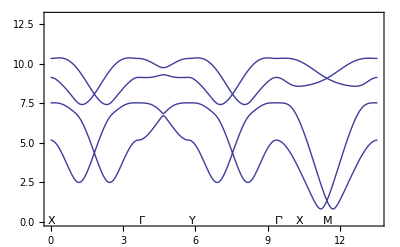

```mathematica
j=-0.5;h=0.63
```

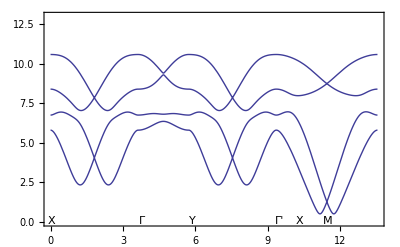

```mathematica
j=0;h=0.63
```

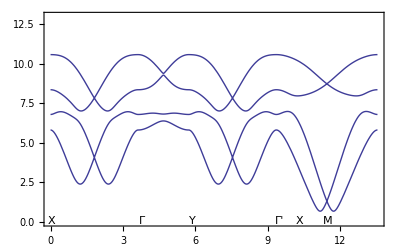

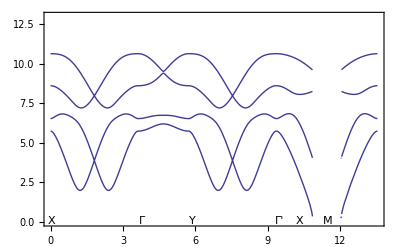

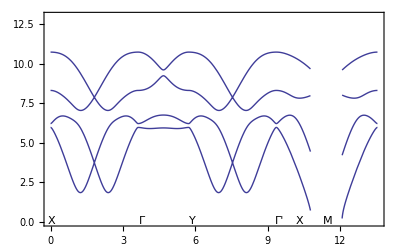

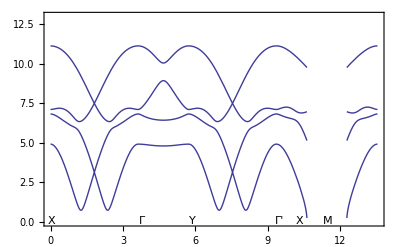

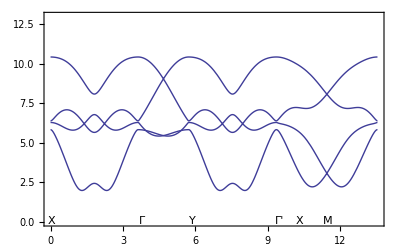

```mathematica
j=0; h=0.6;
```

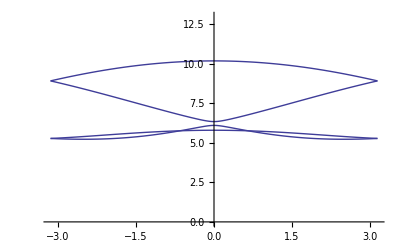

```mathematica
Plot[EE[x,0],{x,-Pi,Pi},PlotRange->{{-Pi,Pi},{0,13}}]
```

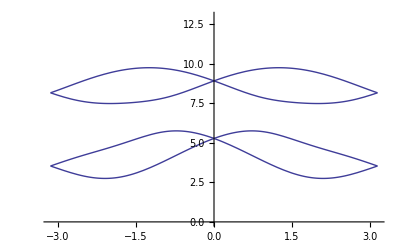

```mathematica
Plot[EE[Pi,x],{x,-Pi,Pi},PlotRange->{{-Pi,Pi},{0,13}}]
```